### Hawk - Dove Game

Define Hawk and Dove expected payoffs

```mathematica
WH=w0+p (v-c)/2+(1-p)v;
WD=w0+(1-p)v/2;
Wbar=p WH+(1-p)WD;
```

Find equilibria

```mathematica
phat=Solve[0==p(1-p)(WH-WD)/Wbar,p]
```

{{p→0},{p→1},{p→v/c}}

When is each stable?

Compare common Dove to rare Hawk

```mathematica
Reduce[{WD>WH,p==0},Reals]
```

v<0&&p==0

Compare common Hawk to rare Dove

```mathematica
Reduce[{WH>WD,p==1},Reals]
```

c<v&&p==1

Use derivative method on internal equilibrium

```mathematica
pprime=p WH/Wbar;
dppdp=D[pprime,p];
```

```mathematica
Simplify[dppdp/.p->v/c]
```

(2 c w0)/(-v^2+c (v+2 w0))

```mathematica
Reduce[{(2 c w0)/(-v^2+c (v+2 w0))<1,w0>0,v>0,c>0,v<c},Reals]
```

v>0&&c>v&&w0>0

Since above is always true, internal equilibrium is stable

Plot recursion

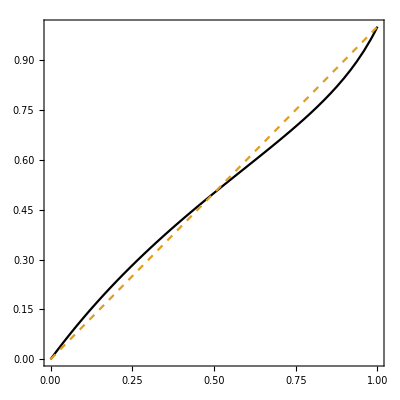

```mathematica
Plot[{p WH/Wbar/.{v->1,c->2,w0->1},p},{p,0,1},Frame->True,AspectRatio->1,PlotStyle->{Black,Dashed}]
```